```mathematica
(*输入系数*)
```

```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
ct=(3*c2+c1)/3;
c4=4c1;
Cc=-2Dc;
MB=1.189;
```

```mathematica
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-q-dleta-up-xi1-L.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;
dHdau=Query[1,3]@dgpdu;
dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;
dEdau=Query[2,3]@dgpdu;
dHdgfu=Interpolation[Flatten[dHdgu,1]];
dHerfu=Interpolation[Flatten[dHeru,1]];

dEdgfu=Interpolation[Flatten[dEdgu,1]];
dEerfu=Interpolation[Flatten[dEeru,1]];
dgpdd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-q-dleta-dp-xi1-L.wdx"];
dHdgd=Query[1,1]@dgpdd;
dHerd=Query[1,2]@dgpdd;
dHdad=Query[1,3]@dgpdd;
dEdgd=Query[2,1]@dgpdd;
dEerd=Query[2,2]@dgpdd;
dEdad=Query[2,3]@dgpdd;
dHdgfd=Interpolation[Flatten[dHdgd,1]];
dHerfd=Interpolation[Flatten[dHerd,1]];

dEdgfd=Interpolation[Flatten[dEdgd,1]];
dEerfd=Interpolation[Flatten[dEerd,1]];
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-q-up-xi1-L.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgfu=Interpolation[Flatten[Hdgu,1]];
Herfu=Interpolation[Flatten[Heru,1]];
Hdafu=Interpolation[Flatten[Hdau,1]];
Edgfu=Interpolation[Flatten[Edgu,1]];
Eerfu=Interpolation[Flatten[Eeru,1]];
Edafu=Interpolation[Flatten[Edau,1]];
gpdd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-q-dp-xi1-L.wdx"];
Hdgd=Query[1,1]@gpdd;
Herd=Query[1,2]@gpdd;
Hdad=Query[1,3]@gpdd;
Edgd=Query[2,1]@gpdd;
Eerd=Query[2,2]@gpdd;
Edad=Query[2,3]@gpdd;
Hdgfd=Interpolation[Flatten[Hdgd,1]];
Herfd=Interpolation[Flatten[Herd,1]];
Hdafd=Interpolation[Flatten[Hdad,1]];
Edgfd=Interpolation[Flatten[Edgd,1]];
Eerfd=Interpolation[Flatten[Eerd,1]];
Edafd=Interpolation[Flatten[Edad,1]];
Dtermu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-q-D-up-xi1-L.wdx"];
HerDu=Query[1,1]@Dtermu;
HdaDu=Query[1,2]@Dtermu;

EerDu=Query[2,1]@Dtermu;
EdaDu=Query[2,2]@Dtermu;
HerDfu=Interpolation[Flatten[HerDu,1]];
HdaDfu=Interpolation[Flatten[HdaDu,1]];

EerDfu=Interpolation[Flatten[EerDu,1]];
EdaDfu=Interpolation[Flatten[EdaDu,1]];
Dtermd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-q-D-dp-xi1-L.wdx"];
HerDd=Query[1,1]@Dtermd;
HdaDd=Query[1,2]@Dtermd;

EerDd=Query[2,1]@Dtermd;
EdaDd=Query[2,2]@Dtermd;
HerDfd=Interpolation[Flatten[HerDd,1]];
HdaDfd=Interpolation[Flatten[HdaDd,1]];

EerDfd=Interpolation[Flatten[EerDd,1]];
EdaDfd=Interpolation[Flatten[EdaDd,1]];
deDtermd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-q-dleta-D-dp-xi1-L.wdx"];
deHerDd=Query[1,1]@deDtermd;

deEerDd=Query[2,1]@deDtermd;
deHerDfd=Interpolation[Flatten[deHerDd,1]];
deEerDfd=Interpolation[Flatten[deEerDd,1]];
deDtermu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-q-dleta-D-up-xi1-L.wdx"];
deHerDu=Query[1,1]@deDtermu;

deEerDu=Query[2,1]@deDtermu;
deHerDfu=Interpolation[Flatten[deHerDu,1]];
deEerDfu=Interpolation[Flatten[deEerDu,1]];
```

```mathematica
Hdgf1u[x_,t_]:=Chop[Hdgfu[x,t],10^-7];
Herf1u[x_,t_]:=Chop[Herfu[x,t],10^-7]+Chop[Hdafu[x,t],10^-7];
Edgf1u[x_,t_]:=Chop[Edgfu[x,t],10^-7];
Eerf1u[x_,t_]:=Chop[Eerfu[x,t],10^-7]+Chop[Edafu[x,t],10^-7];
Hdgf1d[x_,t_]:=Chop[Hdgfd[x,t],10^-7];
Herf1d[x_,t_]:=Chop[Herfd[x,t],10^-7]+Chop[Hdafd[x,t],10^-7];
Edgf1d[x_,t_]:=Chop[Edgfd[x,t],10^-7];
Eerf1d[x_,t_]:=Chop[Eerfd[x,t],10^-7]+Chop[Edafd[x,t],10^-7];
HerDf1d[x_,t_]:=Chop[HerDfd[x,t],10^-7]+Chop[HdaDfd[x,t],10^-7];EerDf1d[x_,t_]:=Chop[EerDfd[x,t],10^-7]+Chop[EdaDfd[x,t],10^-7];
HerDf1u[x_,t_]:=Chop[HerDfu[x,t],10^-7]+Chop[HdaDfu[x,t],10^-7];EerDf1u[x_,t_]:=Chop[EerDfu[x,t],10^-7]+Chop[EdaDfu[x,t],10^-7];
```

```mathematica
(*original result fron the calculation*)
```

```mathematica
Hdgfnu[x_,t_]:=Hdgf1u[x,-t]+dHdgfu[x,-t];
Herfnu[x_,t_]:=Herf1u[x,-t]+dHerfu[x,-t]+HerDf1u[x,-t]+deHerDfu[x,-t];
Edgfnu[x_,t_]:=Edgf1u[x,-t]+dEdgfu[x,-t];
Eerfnu[x_,t_]:=Eerf1u[x,-t]+dEerfu[x,-t]-EerDf1u[x,-t]-deEerDfu[x,-t];
```

```mathematica
Hdgfnd[x_,t_]:=Hdgf1d[x,-t]+dHdgfd[x,-t];
Herfnd[x_,t_]:=Herf1d[x,-t]+dHerfd[x,-t]+HerDf1d[x,-t]+deHerDfd[x,-t];
Edgfnd[x_,t_]:=Edgf1d[x,-t]+dEdgfd[x,-t];
Eerfnd[x_,t_]:=Eerf1d[x,-t]+dEerfd[x,-t]-EerDf1d[x,-t]-deEerDfd[x,-t];
```

```mathematica
(*result of pΔ+ pi0 as input without coe 作为transiton计算中的基础GPD组合*)
```

```mathematica
Hdgud[x_,t_]:=((√2/3)Hdgfnu[x,t]-(2√2/3)Hdgfnd[x,t]);
Herud[x_,t_]:=((√2/3)Herfnu[x,t]-(2√2/3)Herfnd[x,t]);
Edgud[x_,t_]:=((√2/3)Edgfnu[x,t]-(2√2/3)Edgfnd[x,t]);
Eerud[x_,t_]:=((√2/3)Eerfnu[x,t]-(2√2/3)Eerfnd[x,t]);

Hdgdd[x_,t_]:=-((√2/3)Hdgfnu[x,t]-(2√2/3)Hdgfnd[x,t]);
Herdd[x_,t_]:=-((√2/3)Herfnu[x,t]-(2√2/3)Herfnd[x,t]);
Edgdd[x_,t_]:=-((√2/3)Edgfnu[x,t]-(2√2/3)Edgfnd[x,t]);
Eerdd[x_,t_]:=-((√2/3)Eerfnu[x,t]-(2√2/3)Eerfnd[x,t]);
```

```mathematica
Eu=1.6699999468721227;
Ed=-2.029999921595019;
```

```mathematica
EupD=(√2/3)*(Eu-2Ed);
EdpD=-EupD;
```

```mathematica
(*k+ Σ*0 Λ*)
```

```mathematica
coLs0u=(c4/2)/((-√3/2)*EupD);
coLs0d=(-c4/2)/((√3/2)EupD);
coLs0s=0;
```

```mathematica
slCoe=(I)*(1/(2*(2π)^4*fc^2))*((-1)*(Dc+3Fc)*(-Cc)/(√12*4MB*√12));
```

```mathematica
slHdgu[x_,t_]:=(-√3/2)*slCoe*Hdgud[x,t];
slHeru[x_,t_]:=(-√3/2)*slCoe*Herud[x,t];
slEdgu[x_,t_]:=(-√3/2)*slCoe*coLs0u*Edgud[x,t];
slEeru[x_,t_]:=(-√3/2)*slCoe*coLs0u*Eerud[x,t];

slHdgd[x_,t_]:=(√3/2)*slCoe*Hdgud[x,t];
slHerd[x_,t_]:=(√3/2)*slCoe*Herud[x,t];
slEdgd[x_,t_]:=(√3/2)*slCoe*coLs0d*Edgud[x,t];
slEerd[x_,t_]:=(√3/2)*slCoe*coLs0d*Eerud[x,t];
```

```mathematica
(*whole result*)
```

```mathematica
Hdguall[x_,t_]:=slHdgu[x,t];
Heruall[x_,t_]:=slHeru[x,t];
Edguall[x_,t_]:=slEdgu[x,t];
Eeruall[x_,t_]:=slEeru[x,t];

Hdgdall[x_,t_]:=slHdgd[x,t];
Herdall[x_,t_]:=slHerd[x,t];
Edgdall[x_,t_]:=slEdgd[x,t];
Eerdall[x_,t_]:=slEerd[x,t];
```

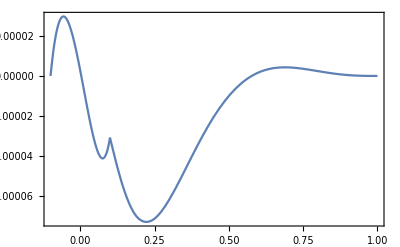
-Graphics-H_dxdiagram p

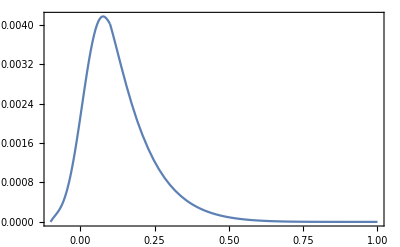
-Graphics-E_dxdiagram q

```mathematica
pHd2d=Labeled[Show[Plot[Hdgdall[x,1],{x,0.1,1},PlotRange->All],Plot[Herdall[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d","x","diagram p"},{Left,Bottom,Top},LabelStyle->24]
pEd2d=Labeled[Show[Plot[Edgdall[x,1],{x,0.1,1},PlotRange->All],Plot[Eerdall[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d","x","diagram q"},{Left,Bottom,Top},LabelStyle->24]
```

```mathematica
pHd2d=Labeled[Show[Plot[Hdgsall[x,1],{x,0.1,1},PlotRange->All],Plot[Hersall[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_s","x","diagram q"},{Left,Bottom,Top},LabelStyle->24]
pEd2d=Labeled[Show[Plot[Edgsall[x,1],{x,0.1,1},PlotRange->All],Plot[Eersall[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_s","x","diagram q"},{Left,Bottom,Top},LabelStyle->24]
```

-Graphics-H_sxdiagram q

-Graphics-E_sxdiagram q

```mathematica
pathu=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"u-diagram-q-L.wdx"}];
pathd=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"d-diagram-q-L.wdx"}];
paths=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"s-diagram-q-L.wdx"}];
outu=<|"H"-><|"DG"->Hdguall[x,t],"ER"->Heruall[x,t]|>,"E"-><|"DG"->Edguall[x,t],"ER"->Eeruall[x,t]|>|>;
outd=<|"H"-><|"DG"->Hdgdall[x,t],"ER"->Herdall[x,t]|>,"E"-><|"DG"->Edgdall[x,t],"ER"->Eerdall[x,t]|>|>;

Export[pathu,outu]
Export[pathd,outd]
```

G:\calc-online\gpd\drawpic\baryon\gpd\result\u-diagram-q-L.wdx

G:\calc-online\gpd\drawpic\baryon\gpd\result\d-diagram-q-L.wdx